```mathematica
ϕ(*rad*)=0. Degree;
ωq(*GHz*)=4.555;
ω(*GHz*)=4.550;
Δ(*GHz*)=ω-ωq;
Ω(*GHz*)=0.043;
Λ(*GHz*)=Abs[Ω+ⅈ Δ];
{nx,ny,nz}={Ω Sin [ϕ],Ω Cos [ϕ],Δ}/Λ
Print["Detuning frequency is "<>ToString[10^3 Δ]<>" MHz."]
Print["Rabi frequency is "<>ToString[10^3 Λ]<>" MHz."]
θ=1/2 ω t;
θ2=1/2 Λ t;
```

{0.,0.993307,-0.115501}

Detuning frequency is -5. MHz.

Rabi frequency is 43.2897 MHz.

```mathematica
U00=(Cos[θ2]-ⅈ nz Sin[θ2]);
U10=(ny-ⅈ nx )Sin[θ2];
```

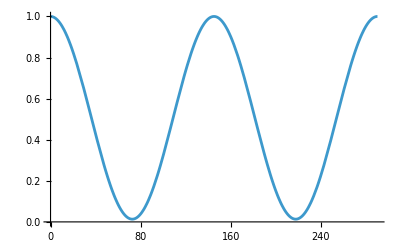

```mathematica
Plot[Abs[U00]^2,{t,0,2(2π)/Λ}]
```

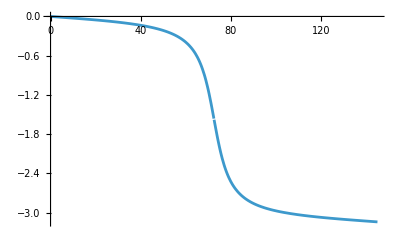

```mathematica
Plot[{Arg[U10]-Arg[U00]},{t,0,1(2π)/Λ},PlotRange->All]
```

```mathematica
axeslabelpos=1.1;
axescolors={Red,Green//Darker,Blue};
blochvectorcolor=Purple;
```

```mathematica
Manipulate[
(*Bloch angles:*)
α(*rad*)=2ArcCos[Abs[U00/.t->t0]];
β=(Arg[U10/.t->t0]-Arg[U00/.t->t0]);
{Blochx,Blochy,Blochz}={Sin[α]Cos[β],Sin[α]Sin[β],Cos[α]};
TableForm[{{
Graphics3D[{
Opacity[.3],
Cyan,Sphere[{0,0,0},{1}],
axescolors[[1]],Line[{{-1,0,0},{1,0,0}}],
axescolors[[2]],Line[{{0,-1,0},{0,1,0}}],
axescolors[[3]],Line[{{0,0,-1},{0,0,1}}],
Opacity[1],
Gray,
Line[Table[{Cos[θ],Sin[θ],0},{θ,0,2π,(2π)/40}]],
Thickness[0.01],blochvectorcolor,
Arrow[{{0,0,0},{Blochx,Blochy,Blochz}}],
axescolors[[1]],Text["x",{axeslabelpos,0,0}],
axescolors[[2]],Text["y",{0,axeslabelpos,0}],
axescolors[[3]],Text["z",{0,0,axislabelpos}]
}
,Boxed->False,ViewPoint->{1.3, 2.4, 1.5}]},{Show[{Plot[Abs[U00]^2,{t,0,(2π)/Λ},PlotStyle->Thin],ListPlot[{{Mod[t0,(2π)/Λ],(Abs[U00]^2/.t->t0)}},PlotStyle->Directive[blochvectorcolor,PointSize[0.05]]]}]}}],{t0,0,(2π)/Λ,1}]
```

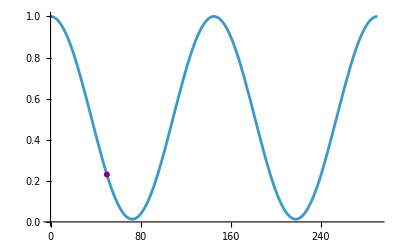

```mathematica
Show[{Plot[Abs[U00]^2,{t,0,2(2π)/Λ}],ListPlot[{{t0,(Abs[U00]^2/.t->t0)}},PlotStyle->Directive[blochvectorcolor,PointSize[0.01]]]}]
```

```mathematica
Mod[341,320.5]
```

20.5

```mathematica
t0=50
```

50

```mathematica
{{t0,(Abs[U00]^2/.t->t0)}}
```

{{5,0.988489}}